```mathematica
$MinPrecision=50;
```

```mathematica
G=1/((3*10^5)^2);
ϵ="e";μ="μ";τ="τ";

Subscript[f, π]=130;
Subscript[V, ud]=0.974;
Subscript[M, ϵ]=0.511; Subscript[M, μ]=105; Subscript[M, τ]=1777;Subscript[M, π0]=135;Subscript[M, π]=139.5;
γ[m_]:=(G^2 m^5)/(192 π^3);
Γννν[m_]:=γ[m](Subscript[θ, ϵ]^2+Subscript[θ, μ]^2+Subscript[θ, τ]^2);
Γllν[m_,α_,α_]:=Return[0];
Γllν[m_,α_,β_]:=If[Subscript[M, α]+Subscript[M, β]<m,1,0]γ[m] Subscript[θ, α]^2(1-8 x^2+8 x^6-x^8-12 x^4 Log[x^2])/.x->Max[Subscript[M, α],Subscript[M, β]]/m;

w=0.2397;
Subscript[C, 1]=1/4(1-4w+8 w^2); Subscript[C, 3]=1/4(1+4w+8 w^2);
Subscript[C, 2]=1/2 w(2w-1); Subscript[C, 4]=1/2 w(2w+1);
L[x_]:=Log[(1-3 x^2-(1-x^2)√(1-4 x^2))/(x^2(1+√(1-4 x^2)))];
Γνll[m_,α_,β_]:=If[Subscript[M, α]+Subscript[M, β]<m,1,0]γ[m] Subscript[θ, α]^2(
If[α≠β,Subscript[C, 1],Subscript[C, 3]]((1-14 x^2-2 x^4-12 x^6)√(1-4 x^2)+12 x^4(x^4-1)L[x])+
4If[α≠β,Subscript[C, 2],Subscript[C, 4]](x^2(2+10 x^2-12 x^4)√(1-4 x^2)+6 x^4(1-2 x^2+2 x^4)L[x])
)/.x->SetAccuracy[Subscript[M, β]/m,100];
Γπν[m_,α_]:=If[Subscript[M, π0]<m,1,0] Subscript[θ, α]^2/(32π)G^2 Subscript[f, π]^2 m^3(1-Subscript[M, π0]^2/m^2)^2;
Γπl[m_,α_]:=If[Subscript[M, π]+Subscript[M, α]<m,1,0] Subscript[θ, α]^2/(16π)G^2 Subscript[V, ud]^2 Subscript[f, π]^2 m^3((1-Subscript[M, α]^2/m^2)^2-Subscript[M, π]^2/m^2(1+Subscript[M, α]^2/m^2))√((1-(Subscript[M, π]-Subscript[M, α])^2/m^2)(1-(Subscript[M, π]+Subscript[M, α])^2/m^2));
```

```mathematica
Γ[m_]:=2Re[
Γννν[m]+(
Total[Γllν[m,#⟦1⟧,#⟦2⟧]+Γνll[m,#⟦1⟧,#⟦2⟧]&/@Tuples[{ϵ,μ,τ},2]]
)+(
Total[Γπν[m,#]+Γπl[m,#]&/@{ϵ,μ,τ}]
)
];
```

```mathematica
MEVtoSEC[mev_]:=(6.582 10^-22)/mev;
```

```mathematica
θs[z_:1]:={Subscript[θ, ϵ]->z/(√m)√(1.3 10^-8),Subscript[θ, μ]->z/(√m)√(3.8 10^-7),Subscript[θ, τ]->z/(√m)√(3.2 10^-7)}
(*θs[z_:1]:={Subscript[θ, ϵ]->0,Subscript[θ, μ]->0,Subscript[θ, τ]->z/(√m)√(33.9 10^-3)}*)
```

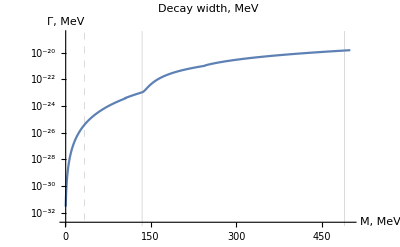
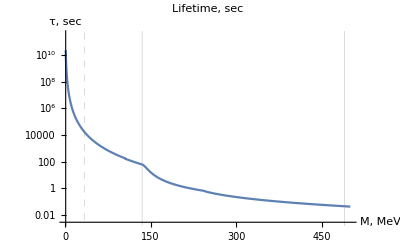

16669.7

```mathematica
Row[{LogPlot[Γ[m]/.θs[],{m,1,500},PlotRange->All,PlotLabel->"Decay width, MeV",AxesLabel->{"M, MeV","Γ, MeV"},PlotPoints->150,ImageSize->400,GridLines->{{{33.9,Dashed},135,490},{}}],
LogPlot[MEVtoSEC[Γ[m]/.θs[]],{m,1,500},PlotRange->All,PlotLabel->"Lifetime, sec",AxesLabel->{"M, MeV","τ, sec"},PlotPoints->150,ImageSize->400,GridLines->{{{33.9,Dashed},135,490},{}}]
}]
MEVtoSEC[Γ[m]/.θs[]]/.m->33.9
```

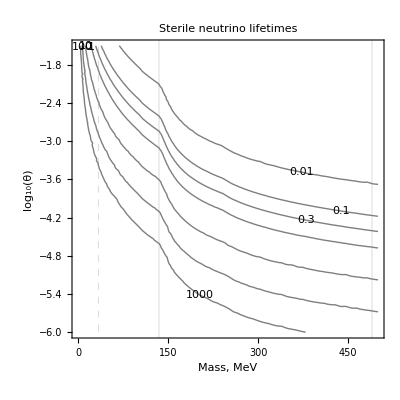

```mathematica
LogarithmicScaling[x_,min_,max_]:=Log[x/min]/Log[max/min];
Show[
ContourPlot[
(MEVtoSEC[Γ[m]]/.θs[10^(y+4)]),
{m,00,500},{y,-6,-1.5},
Contours->{0.01,0.1,0.3,1,10,100,1000},
ContourLabels->All,
ColorFunctionScaling->False,ContourShading->None
],GridLines->{{{33.9,Dashed},135,490},{}},
PlotLabel->"Sterile neutrino lifetimes",
FrameLabel->{"Mass, MeV","log_10(θ)"}
]
```

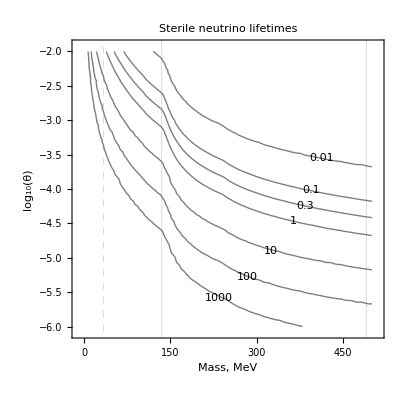

```mathematica
Γγ[m_,T_]:=NIntegrate[T^4/m(e^2 √(e^2-(m/T)^2))/(E^e+1),{e,m/T,∞}];
Plot3D[Γγ[m,T],{T,300,1},{m,135,490}]
```

-Graphics3D-

NIntegrate::inumr: The integrand 150\ p^2/(1 + ⅇ^√90000 + Power[« 2 »]/T)\ √90000 + p^2\ π^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand p^2/2\ (1 + ⅇ^√90000 + Power[« 2 »]/T)\ π^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

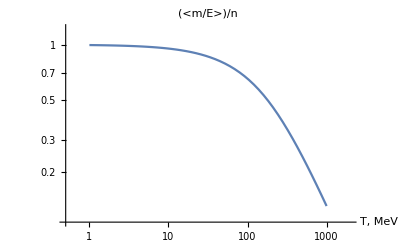

```mathematica
RelativisticCorrection[m_]:=(
LogLogPlot[
NIntegrate[(m p^2)/(2 π^2)1/(√(p^2+m^2))1/(E^((√(p^2+m^2))/T)+1),{p,0,∞}]/NIntegrate[p^2/(2 π^2)1/(E^((√(p^2+m^2))/T)+1),{p,0,∞}],
{T,1000,1},PlotLabel->"(<m/E>)/n",AxesLabel->{"T, MeV"}]
);
RelativisticCorrection[300]
```

```mathematica
Computeθ[m_,t_]:=x/.FindRoot[(MEVtoSEC[Γ[m]/2]/.{Subscript[θ, ϵ]->x,Subscript[θ, μ]->0,Subscript[θ, τ]->0})==t,{x,10^-10}]

data = {{20,0.496257},{20,1.01231},{20,2.02922},{50,0.0901193},{50,0.16007},{80,0.0608292},{80,0.101705},{100,0.0507371},{100,0.100179},{120,0.0507371},{120,0.0848312}};

params={#⟦1⟧,Computeθ[#⟦1⟧,#⟦2⟧],#⟦2⟧}&/@data;
params//MatrixForm
StringJoin["python tests/paper_test/__init__.py --mass "<>ToString[#⟦1⟧]<>" --theta "<>ToString[#⟦2⟧]<>" --comment '_t="<>ToString[#⟦3⟧]<>"'\n"&/@params]
```

(20 | 0.111792 | 0.496257
20 | 0.0782721 | 1.01231
20 | 0.055284 | 2.02922
50 | 0.0265091 | 0.0901193
50 | 0.0198906 | 0.16007
80 | 0.00996268 | 0.0608292
80 | 0.0077048 | 0.101705
100 | 0.00624422 | 0.0507371
100 | 0.00444378 | 0.100179
120 | 0.00395797 | 0.0507371
120 | 0.00306096 | 0.0848312)

python tests/paper_test/__init__.py --mass 20 --theta 0.111792 --comment '_t=0.496257'
python tests/paper_test/__init__.py --mass 20 --theta 0.0782721 --comment '_t=1.01231'
python tests/paper_test/__init__.py --mass 20 --theta 0.055284 --comment '_t=2.02922'
python tests/paper_test/__init__.py --mass 50 --theta 0.0265091 --comment '_t=0.0901193'
python tests/paper_test/__init__.py --mass 50 --theta 0.0198906 --comment '_t=0.16007'
python tests/paper_test/__init__.py --mass 80 --theta 0.00996268 --comment '_t=0.0608292'
python tests/paper_test/__init__.py --mass 80 --theta 0.0077048 --comment '_t=0.101705'
python tests/paper_test/__init__.py --mass 100 --theta 0.00624422 --comment '_t=0.0507371'
python tests/paper_test/__init__.py --mass 100 --theta 0.00444378 --comment '_t=0.100179'
python tests/paper_test/__init__.py --mass 120 --theta 0.00395797 --comment '_t=0.0507371'
python tests/paper_test/__init__.py --mass 120 --theta 0.00306096 --comment '_t=0.0848312'

```mathematica
(*Blahblah*)
{Computeθ[20,1],Computeθ[20,2]}
```

{0.0787524,0.0556863}

```mathematica
{Computeθ[50,0.1],Computeθ[50,0.2]}
```

{0.0177946,0.0125827}

```mathematica
{Computeθ[100,0.05],Computeθ[100,0.1]}
```

{0.00629008,0.00444776}

```mathematica
{Computeθ[100,0.0125],Computeθ[100,0.025]}
```

{0.00889551,0.00629008}

```mathematica
{Computeθ[110,0.0125],Computeθ[110,0.025]}
(MEVtoSEC[Γ[m]]/.{Subscript[θ, ϵ]->#,Subscript[θ, μ]->0,Subscript[θ, τ]->0,m->110})&/@{0.008895512848679276,0.006290077457428593,0.004447756424335316,0.0031450387287135467}
```

{0.00700945,0.00495643}

{0.00776132,0.0155226,0.0310453,0.0620906}

```mathematica
{Computeθ[120,0.07],Computeθ[120,0.05]}
```

{0.00238271,0.00281926}

```mathematica
{Computeθ[120,0.0125],Computeθ[120,0.025]}
```

{0.00563852,0.00398704}

```mathematica
{Computeθ[130,0.0125],Computeθ[130,0.025]}
(MEVtoSEC[Γ[m]]/.{Subscript[θ, ϵ]->#,Subscript[θ, μ]->0,Subscript[θ, τ]->0,m->130})&/@{0.005638524757234747,0.003987039091739609,0.002382711594483937,0.002819262378645064}
```

{0.00461282,0.00326175}

{0.00836587,0.0167317,0.0468489,0.0334635}

```mathematica
{Computeθ[130,0.08], Computeθ[130,0.05]}
```

{0.00257864,0.00326175}

```mathematica
(MEVtoSEC[Γ[m]/2]/.{Subscript[θ, ϵ]->#,Subscript[θ, μ]->0,Subscript[θ, τ]->0,m->20})&/@{0.0556863,0.0393762}
```

{2.,4.}

```mathematica
{Computeθ[80,0.10],Computeθ[80,0.05],Computeθ[80,0.04]}
```

{0.0077702,0.0109887,0.0122858}